```mathematica
(* load in FeynCalc and Hyp Exp *)

Quiet[Needs["HighEnergyPhysics`FeynCalc`"]];
Needs["HypExp`"]
 $LimitTo4=False;
SetOptions[PaVeReduce,Dimension->d];
```

Loading FeynCalc from /Users/Matt/Library/Mathematica/Applications/HighEnergyPhysics

FeynCalc 8.2.0 For help, type ?FeynCalc, open FeynCalcRef8.nb or visit www.feyncalc.org

Loading FeynArts, see www.feynarts.de for documentation

FeynArts 3.7 patched for use with FeynCalc

*-*-*-*-*-* HPL 2.0 *-*-*-*-*-*

Author: Daniel Maitre, University of Zurich

Rules for minimal set loaded for weights: 2, 3, 4, 5, 6.

Rules for minimal set for + - weights loaded for weights: 2, 3, 4, 5, 6.

Table of MZVs loaded up to weight 6

Table of values at I loaded up to weight 6

$HPLFunctions gives a list of the functions of the package.
$HPLOptions gives a list of the options of the package.

More info in hep-ph/0507152, hep-ph/0703052 and at 
 http://krone.physik.unizh.ch/~maitreda/HPL/

***********************************
***********  HypExp 2.0  ************
***********************************
Authors:
 Tobias Huber:  RWTH Aachen,

Daniel Maitre: SLAC, University of Zurich.

HypExp loaded! It allows the expansion of hypergeometric functions around their parameters. 
 The new provided commands are:
 - HypExp
 - HypExpInt
 - HypExpU
 - HypExpAddToLib
 - HypExpIsKnownToOrder

More info in hep-ph/0507094 and at 
 http://krone.physik.unizh.ch/~maitreda/HypExp/

```mathematica
GA[5]
%//StandardForm
```

γ^5

GAD[5]

```mathematica
(* this chunk of code is a small portion of a "header" notebook that I preload into every mathemtica file, just like you preload feyncalc *)
(* I've copy/pasted a select necessary few so it's not a *complete* black box *)

(* formatting *)
eps=ϵ;
delta=δ;
lambda=λ;
sigma=σ;
rho=ρ;
tau=τ;
mu=μ;
p1 /: MakeBoxes[p1,TraditionalForm] = SubscriptBox["p","1"];
p2 /: MakeBoxes[p2,TraditionalForm] = SubscriptBox["p","2"];
p3 /: MakeBoxes[p3,TraditionalForm] = SubscriptBox["p","3"];
p4 /: MakeBoxes[p4,TraditionalForm] = SubscriptBox["p","4"];

(*various lists of momenta -- for some reason necessary *)
listMomOnShell = {p,p1,pn1,pnb1,p2,pn2,pnb2,q,q1,qn1,qnb1,q2,qn2,qnb2,p3,p4}; 
listMomLoop = {k,l};
listMomHeavy={pb};
listMomFull = Join[listMomOnShell,listMomLoop,listMomHeavy];
listNs = {n,nb};
listMomAll = Join[listMomFull,listNs];
altMomLoop = Alternatives@@listMomLoop;
altMomOnShell = Alternatives@@listMomOnShell;
altMomFull = Alternatives@@listMomFull;
altNs = Alternatives@@listNs;
altMomAll = Alternatives@@listMomAll;

(* make any scalar come out of the inner product *)(*it knows a,b commute*) 
SPD /: SPD[a_*b_,c_] /; MatchQ[a,altMomAll]&&!MatchQ[b,altMomAll]:=b*SPD[a,c]; 
Pair /:  Pair[Momentum[a_*b_,D],Momentum[c_,D]] /; MatchQ[a,altMomAll]&&!MatchQ[b,altMomAll]:=b*Pair[Momentum[a,D],Momentum[c,D]] ; 


 (* letting mathemtica know some properties of the momenta *)
SPD /: SPD[0,_] := 0; 
SPD/:SPD[a_,b_+c_]:=SPD[a,b]+SPD[a,c];
SPD/: SPD[p1,p1]:=0;
SPD/: SPD[p4,p4]:=0;
GA/:GA[a_]/;!MatchQ[a,5]:=GAD[a];
DiracGamma/:DiracGamma[Momentum[a_]]/;!MatchQ[a,5]:=DiracGamma[Momentum[a,D],D]=0;

(* extra gamma properties *)
PhatL /:  MakeBoxes[PhatL,TraditionalForm] = SubscriptBox["P̂","L"];
PhatR /:  MakeBoxes[PhatR,TraditionalForm] = SubscriptBox["P̂","R"];
DeclareNonCommutative[PhatL,PhatR];

PhatDef[e_]:=FCE[e]/.{Phatn->nsl.nbsl}/.{Phatnb->nbsl.nsl}/.{PhatL->(1-GA[5])/2}/.{PhatR->(1+GA[5])/2};




(* make a list of massless momenta *)
MasslessQ[expr_] := MatchQ[expr,p|p1|pn1|pnb1|p2|pn2|pnb2|q|q1|qn1|qnb1|q2|qn2|qnb2|n|nb]; 

(* make the list of Feynman variables *)
feynVars={x,y,z,w,x1,y1,z1,w1};
feynmanQ[expr_] := MatchQ[expr,x|y|z|w|x1|y1|z1|w1]; 

FVD/:FVD[a_+b_,c_]:=FVD[a,c]+FVD[b,c]
FVD/:FVD[a_*b_,c_]/;feynmanQ[a]:= a*FVD[b,c];
FVD/:FVD[-a_,b_]:= -FVD[a,b];
Pair/:Pair[LorentzIndex[c_,D],Momentum[a_+b_,D]]:= Pair[LorentzIndex[c,D],Momentum[a,D]]+Pair[LorentzIndex[c,D],Momentum[b,D]];
Pair/:Pair[LorentzIndex[c_,D],Momentum[a_*b_,D]]/;feynmanQ[a]:=a*Pair[LorentzIndex[c,D],Momentum[b,D]];
Pair/:Pair[LorentzIndex[b_,D],Momentum[-a_,D]]:=-Pair[LorentzIndex[b,D],Momentum[a,D]];

SPD /: SPD[a_,a_] /; MasslessQ[a]:= 0; (* apply the on-shell condition for FeynCalc External*)
Pair /: Pair[Momentum[a_,D],Momentum[a_,D]] /; MasslessQ[a]:= 0; (* apply the on-shell condition for FeynCalc Internal *)


expLogs[e_]:=e//.Log[a_/b_]:>Log[a]-Log[b]//.Log[a_*b_]:>Log[a]+Log[b]/.Log[a_^n_]:>  n*Log[a]; 

integrateTermByTerm[e_,{var_,min_,max_}]:=Module[{nterms,expexp,it,iterm,igral,result},

expexp=Expand[e];
nterms=Length[expexp];
it=1;
iterm=0;
igral=0;
result=0;

Print["Integrating ", nterms," terms."]
For[it=1,it≤nterms,it++,
iterm=expexp[[it]];
Print["Term ",it," : ",iterm];
igral=Integrate[iterm,{var,min,max}];
Print["     ",it," : ",igral];
result+=igral;

];

Return[result];


]



$Assumptions=0<y<1&&0<z<1&&eps>0&&0<M<Q&&0<eps<1&&delta>0
```

0<y<1∧0<z<1∧ϵ>0∧0<M<Q∧0<ϵ<1∧δ>0

```mathematica
levi5[a_,b_,c_]:=Module[{ind},LC[a,b,c,ind]GAD[ind].GAD[5]]

cleanIndices[e_,var1_,var2_]:=e/.LC[a_,rho,sigma,b_]:> LC[a,b,rho,sigma]/.f_*LC[a_,b_,rho,sigma]:> (f/.a:>var1/.b:>var2)*LC[var1,var2,rho,sigma]/.f_*Eps[LorentzIndex[a_],LorentzIndex[b_],LorentzIndex[rho],LorentzIndex[sigma]]:>  (f/.a:>var1/.b->var2)*Eps[var1,var2,rho,sigma]
```

### Integral Definitions

```mathematica
(* three propagators, no numerator *)
L0QCDEuclidean[igrand_,deltaSqr_,dim_]:=(Gamma[(6-dim)/2]/((4*Pi)^(dim/2)) )*Inactive[integrateTermByTerm][    Inactive[Integrate][igrand*deltaSqr^((dim-6)/2),{z,0,1-y}]/.x->1-y-z,{y,0,1}]

(* three propagators, l^2 in numerator *)
L2QCDEuclidean[igrand_,deltaSqr_,dim_]:=(D*Gamma[(4-dim)/2]/((4*Pi)^(dim/2)) )*Inactive[integrateTermByTerm][    Inactive[Integrate][igrand*deltaSqr^((dim-4)/2),{z,0,1-y}]/.x->1-y-z,{y,0,1}]
```

### QCD Loop Graphs for 1⊗1

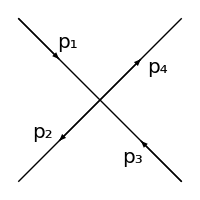

```mathematica
(* reproducting fig 5 of arXiv:0806.1240v2, rotated so time runs left to right*)
Graphics[{ Arrowheads[0.05],  (* --- *) Line[{{-1,-1},{1,1}}],Line[{{-1,1},{1,-1}}] ,Arrow[{{0,0},{0.5,0.5}}] ,Arrow[{{0,0},{-0.5,-0.5}}],Arrow[{{-1,1},{-0.5,0.5}}],Arrow[{{1,-1},{0.5,-0.5}}],
Text[Style[p4,20],{0.7,0.4}],Text[Style[p2,20],{-0.7,-0.4}],Text[Style[p1,20],{-0.4,0.7}],Text[Style[p3,20],{0.4,-0.7}](* --- *)    },ImageSize->200]
```

#### Graph 14

```mathematica
(* here we direct the loop momentum from 4 to 1 *)
```

```mathematica
amplitude14prefac=-I*(TensorProduct["N","N"])*g^2
amplitude14Denominator=(SPD[k,k]-M^2)(SPD[k+p1,k+p1])(SPD[k+p4,k+p4])
amplitude14DiracStructure=SpinorUBar[p4].GAD[mu].GAD[rho].GAD[tau].PhatL.SpinorV[p3]*SpinorVBar[p2].GAD[tau].PhatL.GAD[sigma].GAD[mu].SpinorU[p1]*FVD[k+p4,rhoo]*FVD[k+p1,sigmaa]
(* shifted momentum l equals *)kprime14=k+y*p1+z*p4;
amplitude14DiracStructureShifted=amplitude14DiracStructure/.FVD[k,a_]:> lambda*FVD[l,a]+FVD[(k-kprime14),a]
amplitude14DiracStructureZero=SeriesCoefficient[amplitude14DiracStructureShifted,{lambda,0,0}]
amplitude14DiracStructureTwo=SeriesCoefficient[amplitude14DiracStructureShifted,{lambda,0,2}]
```

-ⅈ g^2 N⊗N

(k^2-M^2) (2 k·p_1+k^2) (2 k·p_4+k^2)

(k^rhoo+p_4^rhoo) (k^sigmaa+p_1^sigmaa) ū(p_4).γ^μ.γ^ρ.γ^τ.(P̂)_L.v(p_3) v̄(p_2).γ^τ.(P̂)_L.γ^σ.γ^μ.u(p_1)

(λ l^rhoo-y p_1^rhoo-z p_4^rhoo+p_4^rhoo) (λ l^sigmaa-y p_1^sigmaa-z p_4^sigmaa+p_1^sigmaa) ū(p_4).γ^μ.γ^ρ.γ^τ.(P̂)_L.v(p_3) v̄(p_2).γ^τ.(P̂)_L.γ^σ.γ^μ.u(p_1)

(-y p_1^rhoo-z p_4^rhoo+p_4^rhoo) (-y p_1^sigmaa-z p_4^sigmaa+p_1^sigmaa) ū(p_4).γ^μ.γ^ρ.γ^τ.(P̂)_L.v(p_3) v̄(p_2).γ^τ.(P̂)_L.γ^σ.γ^μ.u(p_1)

l^rhoo l^sigmaa ū(p_4).γ^μ.γ^ρ.γ^τ.(P̂)_L.v(p_3) v̄(p_2).γ^τ.(P̂)_L.γ^σ.γ^μ.u(p_1)

```mathematica
amplitude14DiracStructureZero(*/.sigmaa->sigma/.rhoo->rho*)//PhatDef//Contract//FCE
%//StandardForm
```

1/4 p_4^rhoo p_1^sigmaa φ(p_4).γ^μ.γ^ρ.γ^τ.(1-γ^5).φ(p_3) φ(p_2).γ^τ.(1-γ^5).γ^σ.γ^μ.φ(p_1)+1/4 y^2 p_1^rhoo p_1^sigmaa φ(p_4).γ^μ.γ^ρ.γ^τ.(1-γ^5).φ(p_3) φ(p_2).γ^τ.(1-γ^5).γ^σ.γ^μ.φ(p_1)-1/4 y p_1^rhoo p_1^sigmaa φ(p_4).γ^μ.γ^ρ.γ^τ.(1-γ^5).φ(p_3) φ(p_2).γ^τ.(1-γ^5).γ^σ.γ^μ.φ(p_1)-1/4 y p_4^rhoo p_1^sigmaa φ(p_4).γ^μ.γ^ρ.γ^τ.(1-γ^5).φ(p_3) φ(p_2).γ^τ.(1-γ^5).γ^σ.γ^μ.φ(p_1)+1/4 y z p_4^rhoo p_1^sigmaa φ(p_4).γ^μ.γ^ρ.γ^τ.(1-γ^5).φ(p_3) φ(p_2).γ^τ.(1-γ^5).γ^σ.γ^μ.φ(p_1)+1/4 y z p_1^rhoo p_4^sigmaa φ(p_4).γ^μ.γ^ρ.γ^τ.(1-γ^5).φ(p_3) φ(p_2).γ^τ.(1-γ^5).γ^σ.γ^μ.φ(p_1)+1/4 z^2 p_4^rhoo p_4^sigmaa φ(p_4).γ^μ.γ^ρ.γ^τ.(1-γ^5).φ(p_3) φ(p_2).γ^τ.(1-γ^5).γ^σ.γ^μ.φ(p_1)-1/4 z p_4^rhoo p_1^sigmaa φ(p_4).γ^μ.γ^ρ.γ^τ.(1-γ^5).φ(p_3) φ(p_2).γ^τ.(1-γ^5).γ^σ.γ^μ.φ(p_1)-1/4 z p_4^rhoo p_4^sigmaa φ(p_4).γ^μ.γ^ρ.γ^τ.(1-γ^5).φ(p_3) φ(p_2).γ^τ.(1-γ^5).γ^σ.γ^μ.φ(p_1)

-1/4 y Spinor[Momentum[p2],0,1].GAD[τ].(1-GAD[5]).GAD[σ].GAD[μ].Spinor[Momentum[p1],0,1] Spinor[Momentum[p4],0,1].GAD[μ].GAD[ρ].GAD[τ].(1-GAD[5]).Spinor[Momentum[p3],0,1] FVD[p1,rhoo] FVD[p1,sigmaa]+1/4 y^2 Spinor[Momentum[p2],0,1].GAD[τ].(1-GAD[5]).GAD[σ].GAD[μ].Spinor[Momentum[p1],0,1] Spinor[Momentum[p4],0,1].GAD[μ].GAD[ρ].GAD[τ].(1-GAD[5]).Spinor[Momentum[p3],0,1] FVD[p1,rhoo] FVD[p1,sigmaa]+1/4 Spinor[Momentum[p2],0,1].GAD[τ].(1-GAD[5]).GAD[σ].GAD[μ].Spinor[Momentum[p1],0,1] Spinor[Momentum[p4],0,1].GAD[μ].GAD[ρ].GAD[τ].(1-GAD[5]).Spinor[Momentum[p3],0,1] FVD[p1,sigmaa] FVD[p4,rhoo]-1/4 y Spinor[Momentum[p2],0,1].GAD[τ].(1-GAD[5]).GAD[σ].GAD[μ].Spinor[Momentum[p1],0,1] Spinor[Momentum[p4],0,1].GAD[μ].GAD[ρ].GAD[τ].(1-GAD[5]).Spinor[Momentum[p3],0,1] FVD[p1,sigmaa] FVD[p4,rhoo]-1/4 z Spinor[Momentum[p2],0,1].GAD[τ].(1-GAD[5]).GAD[σ].GAD[μ].Spinor[Momentum[p1],0,1] Spinor[Momentum[p4],0,1].GAD[μ].GAD[ρ].GAD[τ].(1-GAD[5]).Spinor[Momentum[p3],0,1] FVD[p1,sigmaa] FVD[p4,rhoo]+1/4 y z Spinor[Momentum[p2],0,1].GAD[τ].(1-GAD[5]).GAD[σ].GAD[μ].Spinor[Momentum[p1],0,1] Spinor[Momentum[p4],0,1].GAD[μ].GAD[ρ].GAD[τ].(1-GAD[5]).Spinor[Momentum[p3],0,1] FVD[p1,sigmaa] FVD[p4,rhoo]+1/4 y z Spinor[Momentum[p2],0,1].GAD[τ].(1-GAD[5]).GAD[σ].GAD[μ].Spinor[Momentum[p1],0,1] Spinor[Momentum[p4],0,1].GAD[μ].GAD[ρ].GAD[τ].(1-GAD[5]).Spinor[Momentum[p3],0,1] FVD[p1,rhoo] FVD[p4,sigmaa]-1/4 z Spinor[Momentum[p2],0,1].GAD[τ].(1-GAD[5]).GAD[σ].GAD[μ].Spinor[Momentum[p1],0,1] Spinor[Momentum[p4],0,1].GAD[μ].GAD[ρ].GAD[τ].(1-GAD[5]).Spinor[Momentum[p3],0,1] FVD[p4,rhoo] FVD[p4,sigmaa]+1/4 z^2 Spinor[Momentum[p2],0,1].GAD[τ].(1-GAD[5]).GAD[σ].GAD[μ].Spinor[Momentum[p1],0,1] Spinor[Momentum[p4],0,1].GAD[μ].GAD[ρ].GAD[τ].(1-GAD[5]).Spinor[Momentum[p3],0,1] FVD[p4,rhoo] FVD[p4,sigmaa]

```mathematica
amplitude14DiracStructureZero(*/.sigmaa->sigma/.rhoo->rho*)//PhatDef//Contract//FCE
%//DiracSimplify//FCE
(*%/.GAD[tau,a_,mu]:>DiracMatrix[tau,a,mu]/.GAD[mu,a_,tau]:>DiracMatrix[mu,a,tau]//DiracReduce//FCE*)

%/.GAD[tau].GAD[a_].GAD[mu]:> MTD[tau,a]GAD[mu]+GAD[tau] MTD[a,mu]- MTD[tau,mu]GAD[a]+I*levi5[tau,a,mu]  (* the 3-gamma identity, with gamma5 in D=4 *)
%/.GAD[mu].GAD[a_].GAD[tau]:> MTD[mu,a]GAD[tau]+GAD[mu] MTD[a,tau]- MTD[mu,tau]GAD[a]+I*levi5[mu,a,tau]  (* the 3-gamma identity, with gamma5 in D=4 *)

midCalc=%//DiracSimplify//FCE

midCalc/.GA[a_]:>GAD[a]/.MT[a_,b_]:> MTD[a,b]/.Spinor[a___].GAD[b_].Spinor[c___]:> Spinor[a].(2*GAD[b].Inactive[GAD[AL]]+GAD[b].GAD[5]).Spinor[c]//DiracSimplify//FCE
%/.MT[a_,b_]:> MTD[a,b]/.Inactive[GAD[AL]]->PhatL
cleanIndices[%,xi1,xi2]/.Spinor[a___].GAD[e_].PhatL.Spinor[b___]*Spinor[c___].GAD[e_].PhatL.Spinor[d___]->M0/.sigmaa->sigma/.rhoo->rho//DiracSimplify//FCE
zeroth14Term=%/.GAD[a_].GAD[5]-> GAD[tau].GAD[5]/.GAD[a_].PhatL-> GAD[tau].PhatL//DiracSimplify//FCE
```

1/4 p_4^rhoo p_1^sigmaa φ(p_4).γ^μ.γ^ρ.γ^τ.(1-γ^5).φ(p_3) φ(p_2).γ^τ.(1-γ^5).γ^σ.γ^μ.φ(p_1)+1/4 y^2 p_1^rhoo p_1^sigmaa φ(p_4).γ^μ.γ^ρ.γ^τ.(1-γ^5).φ(p_3) φ(p_2).γ^τ.(1-γ^5).γ^σ.γ^μ.φ(p_1)-1/4 y p_1^rhoo p_1^sigmaa φ(p_4).γ^μ.γ^ρ.γ^τ.(1-γ^5).φ(p_3) φ(p_2).γ^τ.(1-γ^5).γ^σ.γ^μ.φ(p_1)-1/4 y p_4^rhoo p_1^sigmaa φ(p_4).γ^μ.γ^ρ.γ^τ.(1-γ^5).φ(p_3) φ(p_2).γ^τ.(1-γ^5).γ^σ.γ^μ.φ(p_1)+1/4 y z p_4^rhoo p_1^sigmaa φ(p_4).γ^μ.γ^ρ.γ^τ.(1-γ^5).φ(p_3) φ(p_2).γ^τ.(1-γ^5).γ^σ.γ^μ.φ(p_1)+1/4 y z p_1^rhoo p_4^sigmaa φ(p_4).γ^μ.γ^ρ.γ^τ.(1-γ^5).φ(p_3) φ(p_2).γ^τ.(1-γ^5).γ^σ.γ^μ.φ(p_1)+1/4 z^2 p_4^rhoo p_4^sigmaa φ(p_4).γ^μ.γ^ρ.γ^τ.(1-γ^5).φ(p_3) φ(p_2).γ^τ.(1-γ^5).γ^σ.γ^μ.φ(p_1)-1/4 z p_4^rhoo p_1^sigmaa φ(p_4).γ^μ.γ^ρ.γ^τ.(1-γ^5).φ(p_3) φ(p_2).γ^τ.(1-γ^5).γ^σ.γ^μ.φ(p_1)-1/4 z p_4^rhoo p_4^sigmaa φ(p_4).γ^μ.γ^ρ.γ^τ.(1-γ^5).φ(p_3) φ(p_2).γ^τ.(1-γ^5).γ^σ.γ^μ.φ(p_1)

1/4 φ(p_2).γ^τ.γ^σ.γ^μ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_1^rhoo p_1^sigmaa y^2-1/4 φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) φ(p_2).γ^τ.γ^σ.γ^μ.γ^5.φ(p_1) p_1^rhoo p_1^sigmaa y^2-1/4 φ(p_2).γ^τ.γ^σ.γ^μ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_1^rhoo p_1^sigmaa y^2+1/4 φ(p_2).γ^τ.γ^σ.γ^μ.γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_1^rhoo p_1^sigmaa y^2-1/4 φ(p_2).γ^τ.γ^σ.γ^μ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_1^rhoo p_1^sigmaa y+1/4 φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) φ(p_2).γ^τ.γ^σ.γ^μ.γ^5.φ(p_1) p_1^rhoo p_1^sigmaa y+1/4 φ(p_2).γ^τ.γ^σ.γ^μ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_1^rhoo p_1^sigmaa y-1/4 φ(p_2).γ^τ.γ^σ.γ^μ.γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_1^rhoo p_1^sigmaa y+1/4 z φ(p_2).γ^τ.γ^σ.γ^μ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_1^sigmaa p_4^rhoo y-1/4 φ(p_2).γ^τ.γ^σ.γ^μ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_1^sigmaa p_4^rhoo y-1/4 z φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) φ(p_2).γ^τ.γ^σ.γ^μ.γ^5.φ(p_1) p_1^sigmaa p_4^rhoo y+1/4 φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) φ(p_2).γ^τ.γ^σ.γ^μ.γ^5.φ(p_1) p_1^sigmaa p_4^rhoo y-1/4 z φ(p_2).γ^τ.γ^σ.γ^μ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_1^sigmaa p_4^rhoo y+1/4 φ(p_2).γ^τ.γ^σ.γ^μ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_1^sigmaa p_4^rhoo y+1/4 z φ(p_2).γ^τ.γ^σ.γ^μ.γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_1^sigmaa p_4^rhoo y-1/4 φ(p_2).γ^τ.γ^σ.γ^μ.γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_1^sigmaa p_4^rhoo y+1/4 z φ(p_2).γ^τ.γ^σ.γ^μ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_1^rhoo p_4^sigmaa y-1/4 z φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) φ(p_2).γ^τ.γ^σ.γ^μ.γ^5.φ(p_1) p_1^rhoo p_4^sigmaa y-1/4 z φ(p_2).γ^τ.γ^σ.γ^μ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_1^rhoo p_4^sigmaa y+1/4 z φ(p_2).γ^τ.γ^σ.γ^μ.γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_1^rhoo p_4^sigmaa y-1/4 z φ(p_2).γ^τ.γ^σ.γ^μ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_1^sigmaa p_4^rhoo+1/4 φ(p_2).γ^τ.γ^σ.γ^μ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_1^sigmaa p_4^rhoo+1/4 z φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) φ(p_2).γ^τ.γ^σ.γ^μ.γ^5.φ(p_1) p_1^sigmaa p_4^rhoo-1/4 φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) φ(p_2).γ^τ.γ^σ.γ^μ.γ^5.φ(p_1) p_1^sigmaa p_4^rhoo+1/4 z φ(p_2).γ^τ.γ^σ.γ^μ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_1^sigmaa p_4^rhoo-1/4 φ(p_2).γ^τ.γ^σ.γ^μ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_1^sigmaa p_4^rhoo-1/4 z φ(p_2).γ^τ.γ^σ.γ^μ.γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_1^sigmaa p_4^rhoo+1/4 φ(p_2).γ^τ.γ^σ.γ^μ.γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_1^sigmaa p_4^rhoo+1/4 z^2 φ(p_2).γ^τ.γ^σ.γ^μ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_4^rhoo p_4^sigmaa-1/4 z φ(p_2).γ^τ.γ^σ.γ^μ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_4^rhoo p_4^sigmaa-1/4 z^2 φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) φ(p_2).γ^τ.γ^σ.γ^μ.γ^5.φ(p_1) p_4^rhoo p_4^sigmaa+1/4 z φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) φ(p_2).γ^τ.γ^σ.γ^μ.γ^5.φ(p_1) p_4^rhoo p_4^sigmaa-1/4 z^2 φ(p_2).γ^τ.γ^σ.γ^μ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_4^rhoo p_4^sigmaa+1/4 z φ(p_2).γ^τ.γ^σ.γ^μ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_4^rhoo p_4^sigmaa+1/4 z^2 φ(p_2).γ^τ.γ^σ.γ^μ.γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_4^rhoo p_4^sigmaa-1/4 z φ(p_2).γ^τ.γ^σ.γ^μ.γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_4^rhoo p_4^sigmaa

1/4 φ(p_2).(ⅈ γ^ind$1121.γ^5 ϵ^τσμind$1121+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_1^rhoo p_1^sigmaa y^2-1/4 φ(p_2).(ⅈ γ^ind$1123.γ^5 ϵ^τσμind$1123+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_1^rhoo p_1^sigmaa y^2-1/4 φ(p_2).(ⅈ γ^ind$1125.γ^5 ϵ^τσμind$1125+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_1^rhoo p_1^sigmaa y^2+1/4 φ(p_2).(ⅈ γ^ind$1127.γ^5 ϵ^τσμind$1127+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_1^rhoo p_1^sigmaa y^2-1/4 φ(p_2).(ⅈ γ^ind$1120.γ^5 ϵ^τσμind$1120+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_1^rhoo p_1^sigmaa y+1/4 φ(p_2).(ⅈ γ^ind$1122.γ^5 ϵ^τσμind$1122+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_1^rhoo p_1^sigmaa y+1/4 φ(p_2).(ⅈ γ^ind$1124.γ^5 ϵ^τσμind$1124+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_1^rhoo p_1^sigmaa y-1/4 φ(p_2).(ⅈ γ^ind$1126.γ^5 ϵ^τσμind$1126+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_1^rhoo p_1^sigmaa y-1/4 φ(p_2).(ⅈ γ^ind$1129.γ^5 ϵ^τσμind$1129+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_1^sigmaa p_4^rhoo y+1/4 z φ(p_2).(ⅈ γ^ind$1131.γ^5 ϵ^τσμind$1131+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_1^sigmaa p_4^rhoo y+1/4 φ(p_2).(ⅈ γ^ind$1133.γ^5 ϵ^τσμind$1133+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_1^sigmaa p_4^rhoo y-1/4 z φ(p_2).(ⅈ γ^ind$1135.γ^5 ϵ^τσμind$1135+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_1^sigmaa p_4^rhoo y+1/4 φ(p_2).(ⅈ γ^ind$1137.γ^5 ϵ^τσμind$1137+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_1^sigmaa p_4^rhoo y-1/4 z φ(p_2).(ⅈ γ^ind$1139.γ^5 ϵ^τσμind$1139+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_1^sigmaa p_4^rhoo y-1/4 φ(p_2).(ⅈ γ^ind$1141.γ^5 ϵ^τσμind$1141+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_1^sigmaa p_4^rhoo y+1/4 z φ(p_2).(ⅈ γ^ind$1143.γ^5 ϵ^τσμind$1143+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_1^sigmaa p_4^rhoo y+1/4 z φ(p_2).(ⅈ γ^ind$1144.γ^5 ϵ^τσμind$1144+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_1^rhoo p_4^sigmaa y-1/4 z φ(p_2).(ⅈ γ^ind$1145.γ^5 ϵ^τσμind$1145+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_1^rhoo p_4^sigmaa y-1/4 z φ(p_2).(ⅈ γ^ind$1146.γ^5 ϵ^τσμind$1146+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_1^rhoo p_4^sigmaa y+1/4 z φ(p_2).(ⅈ γ^ind$1147.γ^5 ϵ^τσμind$1147+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_1^rhoo p_4^sigmaa y+1/4 φ(p_2).(ⅈ γ^ind$1128.γ^5 ϵ^τσμind$1128+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_1^sigmaa p_4^rhoo-1/4 z φ(p_2).(ⅈ γ^ind$1130.γ^5 ϵ^τσμind$1130+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_1^sigmaa p_4^rhoo-1/4 φ(p_2).(ⅈ γ^ind$1132.γ^5 ϵ^τσμind$1132+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_1^sigmaa p_4^rhoo+1/4 z φ(p_2).(ⅈ γ^ind$1134.γ^5 ϵ^τσμind$1134+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_1^sigmaa p_4^rhoo-1/4 φ(p_2).(ⅈ γ^ind$1136.γ^5 ϵ^τσμind$1136+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_1^sigmaa p_4^rhoo+1/4 z φ(p_2).(ⅈ γ^ind$1138.γ^5 ϵ^τσμind$1138+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_1^sigmaa p_4^rhoo+1/4 φ(p_2).(ⅈ γ^ind$1140.γ^5 ϵ^τσμind$1140+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_1^sigmaa p_4^rhoo-1/4 z φ(p_2).(ⅈ γ^ind$1142.γ^5 ϵ^τσμind$1142+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_1^sigmaa p_4^rhoo-1/4 z φ(p_2).(ⅈ γ^ind$1148.γ^5 ϵ^τσμind$1148+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_4^rhoo p_4^sigmaa+1/4 z^2 φ(p_2).(ⅈ γ^ind$1149.γ^5 ϵ^τσμind$1149+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_4^rhoo p_4^sigmaa+1/4 z φ(p_2).(ⅈ γ^ind$1150.γ^5 ϵ^τσμind$1150+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_4^rhoo p_4^sigmaa-1/4 z^2 φ(p_2).(ⅈ γ^ind$1151.γ^5 ϵ^τσμind$1151+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_4^rhoo p_4^sigmaa+1/4 z φ(p_2).(ⅈ γ^ind$1152.γ^5 ϵ^τσμind$1152+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_4^rhoo p_4^sigmaa-1/4 z^2 φ(p_2).(ⅈ γ^ind$1153.γ^5 ϵ^τσμind$1153+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_4^rhoo p_4^sigmaa-1/4 z φ(p_2).(ⅈ γ^ind$1154.γ^5 ϵ^τσμind$1154+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_4^rhoo p_4^sigmaa+1/4 z^2 φ(p_2).(ⅈ γ^ind$1155.γ^5 ϵ^τσμind$1155+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_4^rhoo p_4^sigmaa

1/4 φ(p_2).(ⅈ γ^ind$1121.γ^5 ϵ^τσμind$1121+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$1158.γ^5 ϵ^μρτind$1158+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).φ(p_3) p_1^rhoo p_1^sigmaa y^2-1/4 φ(p_4).(ⅈ γ^ind$1160.γ^5 ϵ^μρτind$1160+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).φ(p_3) φ(p_2).(ⅈ γ^ind$1123.γ^5 ϵ^τσμind$1123+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) p_1^rhoo p_1^sigmaa y^2-1/4 φ(p_2).(ⅈ γ^ind$1125.γ^5 ϵ^τσμind$1125+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$1162.γ^5 ϵ^μρτind$1162+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).γ^5.φ(p_3) p_1^rhoo p_1^sigmaa y^2+1/4 φ(p_2).(ⅈ γ^ind$1127.γ^5 ϵ^τσμind$1127+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).(ⅈ γ^ind$1164.γ^5 ϵ^μρτind$1164+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).γ^5.φ(p_3) p_1^rhoo p_1^sigmaa y^2-1/4 φ(p_2).(ⅈ γ^ind$1120.γ^5 ϵ^τσμind$1120+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$1157.γ^5 ϵ^μρτind$1157+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).φ(p_3) p_1^rhoo p_1^sigmaa y+1/4 φ(p_4).(ⅈ γ^ind$1159.γ^5 ϵ^μρτind$1159+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).φ(p_3) φ(p_2).(ⅈ γ^ind$1122.γ^5 ϵ^τσμind$1122+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) p_1^rhoo p_1^sigmaa y+1/4 φ(p_2).(ⅈ γ^ind$1124.γ^5 ϵ^τσμind$1124+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$1161.γ^5 ϵ^μρτind$1161+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).γ^5.φ(p_3) p_1^rhoo p_1^sigmaa y-1/4 φ(p_2).(ⅈ γ^ind$1126.γ^5 ϵ^τσμind$1126+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).(ⅈ γ^ind$1163.γ^5 ϵ^μρτind$1163+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).γ^5.φ(p_3) p_1^rhoo p_1^sigmaa y-1/4 φ(p_2).(ⅈ γ^ind$1129.γ^5 ϵ^τσμind$1129+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$1166.γ^5 ϵ^μρτind$1166+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).φ(p_3) p_1^sigmaa p_4^rhoo y+1/4 z φ(p_2).(ⅈ γ^ind$1131.γ^5 ϵ^τσμind$1131+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$1168.γ^5 ϵ^μρτind$1168+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).φ(p_3) p_1^sigmaa p_4^rhoo y+1/4 φ(p_4).(ⅈ γ^ind$1170.γ^5 ϵ^μρτind$1170+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).φ(p_3) φ(p_2).(ⅈ γ^ind$1133.γ^5 ϵ^τσμind$1133+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) p_1^sigmaa p_4^rhoo y-1/4 z φ(p_4).(ⅈ γ^ind$1172.γ^5 ϵ^μρτind$1172+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).φ(p_3) φ(p_2).(ⅈ γ^ind$1135.γ^5 ϵ^τσμind$1135+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) p_1^sigmaa p_4^rhoo y+1/4 φ(p_2).(ⅈ γ^ind$1137.γ^5 ϵ^τσμind$1137+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$1174.γ^5 ϵ^μρτind$1174+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).γ^5.φ(p_3) p_1^sigmaa p_4^rhoo y-1/4 z φ(p_2).(ⅈ γ^ind$1139.γ^5 ϵ^τσμind$1139+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$1176.γ^5 ϵ^μρτind$1176+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).γ^5.φ(p_3) p_1^sigmaa p_4^rhoo y-1/4 φ(p_2).(ⅈ γ^ind$1141.γ^5 ϵ^τσμind$1141+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).(ⅈ γ^ind$1178.γ^5 ϵ^μρτind$1178+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).γ^5.φ(p_3) p_1^sigmaa p_4^rhoo y+1/4 z φ(p_2).(ⅈ γ^ind$1143.γ^5 ϵ^τσμind$1143+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).(ⅈ γ^ind$1180.γ^5 ϵ^μρτind$1180+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).γ^5.φ(p_3) p_1^sigmaa p_4^rhoo y+1/4 z φ(p_2).(ⅈ γ^ind$1144.γ^5 ϵ^τσμind$1144+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$1181.γ^5 ϵ^μρτind$1181+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).φ(p_3) p_1^rhoo p_4^sigmaa y-1/4 z φ(p_4).(ⅈ γ^ind$1182.γ^5 ϵ^μρτind$1182+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).φ(p_3) φ(p_2).(ⅈ γ^ind$1145.γ^5 ϵ^τσμind$1145+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) p_1^rhoo p_4^sigmaa y-1/4 z φ(p_2).(ⅈ γ^ind$1146.γ^5 ϵ^τσμind$1146+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$1183.γ^5 ϵ^μρτind$1183+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).γ^5.φ(p_3) p_1^rhoo p_4^sigmaa y+1/4 z φ(p_2).(ⅈ γ^ind$1147.γ^5 ϵ^τσμind$1147+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).(ⅈ γ^ind$1184.γ^5 ϵ^μρτind$1184+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).γ^5.φ(p_3) p_1^rhoo p_4^sigmaa y+1/4 φ(p_2).(ⅈ γ^ind$1128.γ^5 ϵ^τσμind$1128+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$1165.γ^5 ϵ^μρτind$1165+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).φ(p_3) p_1^sigmaa p_4^rhoo-1/4 z φ(p_2).(ⅈ γ^ind$1130.γ^5 ϵ^τσμind$1130+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$1167.γ^5 ϵ^μρτind$1167+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).φ(p_3) p_1^sigmaa p_4^rhoo-1/4 φ(p_4).(ⅈ γ^ind$1169.γ^5 ϵ^μρτind$1169+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).φ(p_3) φ(p_2).(ⅈ γ^ind$1132.γ^5 ϵ^τσμind$1132+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) p_1^sigmaa p_4^rhoo+1/4 z φ(p_4).(ⅈ γ^ind$1171.γ^5 ϵ^μρτind$1171+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).φ(p_3) φ(p_2).(ⅈ γ^ind$1134.γ^5 ϵ^τσμind$1134+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) p_1^sigmaa p_4^rhoo-1/4 φ(p_2).(ⅈ γ^ind$1136.γ^5 ϵ^τσμind$1136+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$1173.γ^5 ϵ^μρτind$1173+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).γ^5.φ(p_3) p_1^sigmaa p_4^rhoo+1/4 z φ(p_2).(ⅈ γ^ind$1138.γ^5 ϵ^τσμind$1138+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$1175.γ^5 ϵ^μρτind$1175+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).γ^5.φ(p_3) p_1^sigmaa p_4^rhoo+1/4 φ(p_2).(ⅈ γ^ind$1140.γ^5 ϵ^τσμind$1140+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).(ⅈ γ^ind$1177.γ^5 ϵ^μρτind$1177+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).γ^5.φ(p_3) p_1^sigmaa p_4^rhoo-1/4 z φ(p_2).(ⅈ γ^ind$1142.γ^5 ϵ^τσμind$1142+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).(ⅈ γ^ind$1179.γ^5 ϵ^μρτind$1179+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).γ^5.φ(p_3) p_1^sigmaa p_4^rhoo-1/4 z φ(p_2).(ⅈ γ^ind$1148.γ^5 ϵ^τσμind$1148+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$1185.γ^5 ϵ^μρτind$1185+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).φ(p_3) p_4^rhoo p_4^sigmaa+1/4 z^2 φ(p_2).(ⅈ γ^ind$1149.γ^5 ϵ^τσμind$1149+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$1186.γ^5 ϵ^μρτind$1186+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).φ(p_3) p_4^rhoo p_4^sigmaa+1/4 z φ(p_4).(ⅈ γ^ind$1187.γ^5 ϵ^μρτind$1187+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).φ(p_3) φ(p_2).(ⅈ γ^ind$1150.γ^5 ϵ^τσμind$1150+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) p_4^rhoo p_4^sigmaa-1/4 z^2 φ(p_4).(ⅈ γ^ind$1188.γ^5 ϵ^μρτind$1188+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).φ(p_3) φ(p_2).(ⅈ γ^ind$1151.γ^5 ϵ^τσμind$1151+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) p_4^rhoo p_4^sigmaa+1/4 z φ(p_2).(ⅈ γ^ind$1152.γ^5 ϵ^τσμind$1152+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$1189.γ^5 ϵ^μρτind$1189+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).γ^5.φ(p_3) p_4^rhoo p_4^sigmaa-1/4 z^2 φ(p_2).(ⅈ γ^ind$1153.γ^5 ϵ^τσμind$1153+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$1190.γ^5 ϵ^μρτind$1190+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).γ^5.φ(p_3) p_4^rhoo p_4^sigmaa-1/4 z φ(p_2).(ⅈ γ^ind$1154.γ^5 ϵ^τσμind$1154+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).(ⅈ γ^ind$1191.γ^5 ϵ^μρτind$1191+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).γ^5.φ(p_3) p_4^rhoo p_4^sigmaa+1/4 z^2 φ(p_2).(ⅈ γ^ind$1155.γ^5 ϵ^τσμind$1155+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).(ⅈ γ^ind$1192.γ^5 ϵ^μρτind$1192+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).γ^5.φ(p_3) p_4^rhoo p_4^sigmaa

$Aborted

midCalc

midCalc

midCalc

«1 more identical outputs»

```mathematica
(amplitude14DiracStructureTwo/.rho->alpha/.sigma->alpha/.FVD[l,rhoo]*FVD[l,sigmaa]->SPD[l,l]/D)//PhatDef//Contract//FCE
%//DiracSimplify//FCE
%/.GAD[tau].GAD[a_].GAD[mu]:> MTD[tau,a]GAD[mu]+GAD[tau] MTD[a,mu]- MTD[tau,mu]GAD[a]+I*levi5[tau,a,mu]  (* the 3-gamma identity, with gamma5 in D=4 *)
%/.GAD[mu].GAD[a_].GAD[tau]:> MTD[mu,a]GAD[tau]+GAD[mu] MTD[a,tau]- MTD[mu,tau]GAD[a]+I*levi5[mu,a,tau]  (* the 3-gamma identity, with gamma5 in D=4 *)
%//DiracSimplify//FCE

%/.Spinor[a___].GAD[b_].Spinor[c___]:> Spinor[a].(2*GAD[b].Inactive[GAD[AL]]+GAD[b].GAD[5]).Spinor[c]//DiracSimplify//FCE
%/.Inactive[GAD[AL]]->PhatL
quadratic14Term=%/.Spinor[a___].GAD[e_].PhatL.Spinor[b___]*Spinor[c___].GAD[e_].PhatL.Spinor[d___]->M0/.GAD[a_].GAD[5]-> GAD[tau].GAD[5]/.GAD[a_].PhatL-> GAD[tau].PhatL//Simplify

(* should be 16 L^2/D = D *)
```

```mathematica
(* rah14 =  4 M1 (y-1) (z-1) when D=4 *)
```

```mathematica
(* integrating the zeroth order term *)

cleanIndices[zeroth14Term,xi1,xi2]
%/.sigmaa->sigma/.rhoo->rho//Contract//DiracSimplify//FCE;
%/.GSD[p1].PhatL->PhatR.GSD[p1]/.GSD[p4].PhatL->PhatR.GSD[p4]//Simplify;
(%//DiracSimplify//FCE)/.PhatR.GSD[p1]->GSD[p1].PhatL/.PhatR.GSD[p4]->GSD[p4].PhatL
rah14=%/.GAD[a_].GAD[5]-> GAD[tau].GAD[5]/.GAD[a_].PhatL-> GAD[tau].PhatL/.GSD[p2]->-GSD[p1]/.GSD[p3]->-GSD[p4]/.Spinor[___].a_ .Spinor[___]->Sqrt[M1]//Simplify

L0QCDEuclidean[rah14,x*M^2+SPD[kprime14-k],4-2*eps]//.SPD[a_,b_*z]:>z*SPD[a,b]/.SPD[p4,p4]->0/.SPD[p1,p4]->Q^2/2
FullSimplify[Activate[%,Integrate]/.eps->-eps,Assumptions->M^2≠Q^2*y](* the integral is the same regardless of whether or not this assumption is given *)
preAnswerZero14=Activate[%,integrateTermByTerm]/.eps->-eps

Series[preAnswerZero14//Simplify,{M,0,0}]//Normal
Quiet@Series[-I(* imaginary unit from Wick rotation, -1 from oddness of resulting integrand *)*%*amplitude14prefac/.{g:> Sqrt[4*Pi*alphaMS*(Exp[EulerGamma]*muMS^2/(4*Pi))^((4-D)/2)]}/.D->4-2*eps,{eps,0,0}]//Normal
%//FullSimplify;
%//expLogs//Expand;
answerZero14=FullSimplify[%,Assumptions->M>0&&Q>0&&muMS>0];

answerZero14//expLogs//Expand
%/.Log[M]->LM/2+Log[muMS]/.Log[Q]->Lt/2+Log[muMS]/.alphaMS->alphabar*2*Pi//Expand
simpZero14=%//Expand
```

```mathematica
(* integrating the quadratic term *)

quadratic14Term/.SPD[l,l]->1;
%/.sigmaa->sigma/.rhoo->rho//DiracSimplify//FCE;
%/.GSD[p1].PhatL->PhatR.GSD[p1]/.GSD[p4].PhatL->PhatR.GSD[p4]//Simplify;
rahrah14=(%//DiracSimplify//FCE)/.PhatR.GSD[p1]->GSD[p1].PhatL/.PhatR.GSD[p4]->GSD[p4].PhatL

L2QCDEuclidean[rahrah14,x*M^2+SPD[kprime14-k],4-2*eps]//.SPD[a_,b_*z]:>z*SPD[a,b]/.SPD[p4,p4]->0/.SPD[p1,p4]->Q^2/2
FullSimplify[Activate[%,Integrate]/.eps->-eps,Assumptions->M^2≠Q^2*y](* the integral is the same regardless of whether or not this assumption is given *)
preAnswerQuad14=Activate[%,integrateTermByTerm]/.eps->-eps;

Series[preAnswerQuad14//Simplify,{M,0,0}]//Normal
Quiet@Series[I(* imaginary unit from Wick rotation *)*%*amplitude14prefac/.{g:> Sqrt[4*Pi*alphaMS*(Exp[EulerGamma]*muMS^2/(4*Pi))^((4-D)/2)]}/.D->4-2*eps,{eps,0,0}]//Normal
%//FullSimplify;
%//expLogs//Expand;
answerQuad14=FullSimplify[%,Assumptions->M>0&&Q>0&&muMS>0];

answerQuad14//expLogs//Expand
%/.Log[M]->LM/2+Log[muMS]/.Log[Q]->Lt/2+Log[muMS]/.alphaMS->alphabar*2*Pi//Expand
simpQuad14=%//Expand
```